# Resource-driven disease dynamics: linking resources, traits, trophic cascades, and instability using loop analysis

State Variables:
S => Susceptible host density
F (I) => Infected host density
Z => Propagule density
A => Algal resource density

Parameters: 
ds => loss rate, hosts
dz => loss rate, propagules
e => conversion efficiency
f => feeding rate, fixed slope or maximum
h => half-saturation constant, feeding rate
k1 => carrying capacity, algal resource
o => propagule yield, fixed slope or maximum
r => growth rate, algal resource
u => per propagule infectivity
v => virulent mortality
theta => reduction of feeding rate, infected hosts

### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Quiet[<<"/Users/eden/Desktop/RESEARCH/CODE/Dynamica/Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
Quiet[<<"/Users/eden/Downloads/lce.m"]
```

## FIGURE A1

```mathematica
Clear[ds];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds=0.025;
```

```mathematica
solsT3 = Solve[{dST3==0,dFT3==0,dZT3==0,dAT3==0},{A,S,F,Z},WorkingPrecision->MachinePrecision];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsT3[[5]]/.{k1->3}
```

{A→0.43524+9.99201×10^-16 ⅈ,S→0.126173-5.09553×10^-13 ⅈ,F→38.8352+2.40473×10^-13 ⅈ,Z→819.771+4.98754×10^-12 ⅈ}

```mathematica
saddleT3 = solsT3[[5]]/.ds->0.025;(* evaluated at ds = 0.025*)
```

```mathematica
ASI = -J11T3(J23T3 * J32T3 - J22T3 * J33T3);
ASZ = -J11T3(J24T3 * J42T3 - J22T3 * J44T3);
AIZ = -J11T3(J34T3 * J43T3 - J33T3 * J44T3);
```

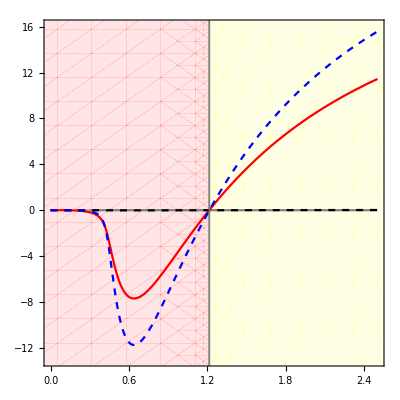

```mathematica
Show[RegionPlot[x<1.214609,{x,-1,4},{y,-20,20}, BoundaryStyle->{Thin,Gray},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Thin,Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Graphics[{Gray,Thick,InfiniteLine[{{1.214609,0},{1.214609,5}}]}],
Plot[Re[ASI/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray}],
Plot[Re[ASZ/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->Red],
Plot[Re[AIZ/.saddleT3/.ds->0.025],{k1,0,2.5},PlotStyle->{Black,Dashed}],
Plot[Re[UL2T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Blue,Dashed}],
PlotRange->{{0,2.5},{-13,16}},AspectRatio->1,LabelStyle->{Black,16},AxesOrigin->{0,-14}
]
```

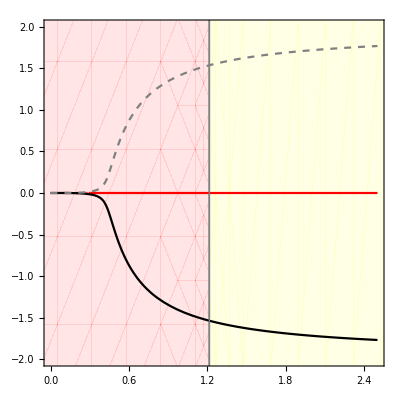

```mathematica
(* ASI *)
Show[
RegionPlot[x<1.214609,{x,-1,4},{y,-10,10}, BoundaryStyle->{Thin,Gray},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-40,40}, BoundaryStyle->{Thin,Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Graphics[{Gray,Thick,InfiniteLine[{{1.214609,0},{1.214609,5}}]}],
Plot[Re[ASI/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Red}],
Plot[Re[-J22T3 * J33T3/.saddleT3/.ds->0.025],{k1,0,2.5},PlotStyle->{Black}],
Plot[Re[J23T3 * J32T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray, Dashed}],
PlotRange->{{0,2.5},{-2,2}},AspectRatio->1,LabelStyle->{Black,16},AxesOrigin->{0,-2}
]
```

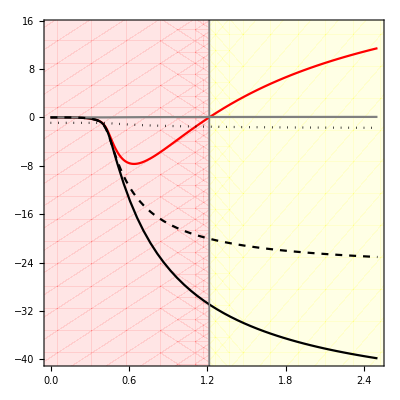

```mathematica
(* ASZ *)
Show[
RegionPlot[x<1.214609,{x,-1,4},{y,-50,20}, BoundaryStyle->{Thin,Gray},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-60,40}, BoundaryStyle->{Thin,Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Graphics[{Gray,Thick,InfiniteLine[{{1.214609,0},{1.214609,5}}]}],
Plot[Re[ASZ/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Red}],
Plot[Re[-J22T3 * J44T3/.saddleT3/.ds->0.025],{k1,0,2.5},PlotStyle->{Black}],
Plot[Re[J24T3 * J42T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray}],
Plot[Re[J22T3 /.saddleT3/.ds->0.025],{k1,0,2.5},PlotStyle->{Black, Dashed}],
Plot[Re[J44T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Black, Dotted}],
PlotRange->{{0,2.5},{-40,15}},AspectRatio->1,LabelStyle->{Black,16},AxesOrigin->{0,-40}
]
```

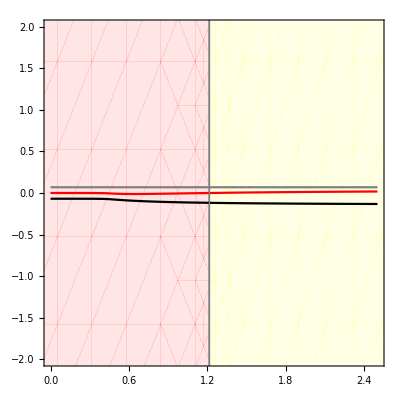

```mathematica
(* AIZ *)
Show[
RegionPlot[x<1.214609,{x,-1,4},{y,-10,10}, BoundaryStyle->{Thin,Gray},PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.214609,{x,0,4},{y,-10,10}, BoundaryStyle->{Thin,Gray},PlotStyle->{Yellow, Opacity[0.1]}],
Graphics[{Gray,Thick,InfiniteLine[{{1.214609,0},{1.214609,5}}]}],
Plot[Re[AIZ/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Red}],
Plot[Re[-J33T3 * J44T3/.saddleT3/.ds->0.025],{k1,0,2.5},PlotStyle->{Black}],
Plot[Re[J34T3 * J43T3/.saddleT3/.ds->0.025],{k1,0,2.5}, PlotStyle->{Gray}],
PlotRange->{{0,2.5},{-2,2}},AspectRatio->1,LabelStyle->{Black,16},AxesOrigin->{0,-1}
]
```

## FIGURE A2

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
parsT3SP = {e -> 8,h->0.2314,f->0.0153,dz->0.9,u->1.049,v->0.05157,o->483.8,r->1,theta->0.8,k1->3};
```

```mathematica
dAT3SP = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*(S+theta*F);
dST3SP= e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S;
dFT3SP=u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F;
dZT3SP=o*((f*A)/(h^2+A^2))*A*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z;
```

### Jacobian Elements & Feedbacks

```mathematica
J11T3SP = FullSimplify[D[dAT3SP,A]];
J12T3SP = FullSimplify[D[dAT3SP,S]];
J13T3SP = FullSimplify[D[dAT3SP,F]];
J14T3SP = FullSimplify[D[dAT3SP,Z]];
```

```mathematica
J21T3SP = FullSimplify[D[dST3SP,A]];
J22T3SP = FullSimplify[D[dST3SP,S]];
J23T3SP = FullSimplify[D[dST3SP,F]];
J24T3SP = FullSimplify[D[dST3SP,Z]];
```

```mathematica
J31T3SP = FullSimplify[D[dFT3SP,A]];
J32T3SP = FullSimplify[D[dFT3SP,S]];
J33T3SP = FullSimplify[D[dFT3SP,F]];
J34T3SP = FullSimplify[D[dFT3SP,Z]];
```

```mathematica
J41T3SP = FullSimplify[D[dZT3SP,A]];
J42T3SP = FullSimplify[D[dZT3SP,S]];
J43T3SP = FullSimplify[D[dZT3SP,F]];
J44T3SP = FullSimplify[D[dZT3SP,Z]];
```

```mathematica
JMT3SP = {{J11T3SP,J12T3SP,J13T3SP,J14T3SP},{J21T3SP,J22T3SP,J23T3SP,J24T3SP},{J31T3SP,J32T3SP,J33T3SP,J34T3SP},{J41T3SP,J42T3SP,J43T3SP,J44T3SP}};
JMT3SP//MatrixForm
```

(r-(2 A r)/k1-(2 A f h^2 (S+F theta))/((A^2+h^2)^2) | -(A^2 f)/(A^2+h^2) | -(A^2 f theta)/(A^2+h^2) | 0
(2 A e f h^2 (S+F theta)+f (A-h) (A+h) S u Z)/((A^2+h^2)^2) | -(A^2 (ds-e f)+ds h^2+A f u Z)/(A^2+h^2) | (A^2 e f theta)/(A^2+h^2) | -(A f S u)/(A^2+h^2)
(f (-A^2+h^2) S u Z)/((A^2+h^2)^2) | (A f u Z)/(A^2+h^2) | -ds-v | (A f S u)/(A^2+h^2)
(2 A f F h^2 o (ds+v)+f (A-h) (A+h) (S+F theta) Z)/((A^2+h^2)^2) | -(A f Z)/(A^2+h^2) | (A f (A o (ds+v)-theta Z))/(A^2+h^2) | -dz-(A f (S+F theta))/(A^2+h^2))

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jAA,jAS,jAF,0},{jSA,jSS,jSF,jSZ},{jFA,jFS,jFF,jFZ},{jZA,jZS,jZF,jZZ}};
DJac//MatrixForm
```

(jAA | jAS | jAF | 0
jSA | jSS | jSF | jSZ
jFA | jFS | jFF | jFZ
jZA | jZS | jZF | jZZ)

```mathematica
Clear[ds];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
k1=3;
theta = 0.8;
```

```mathematica
solsT3SP = Solve[{dST3SP==0,dFT3SP==0,dZT3SP==0,dAT3SP==0},{A,S,F,Z},WorkingPrecision->MachinePrecision];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsT3SP[[8]]/.{ds->0.025}
```

{A→0.217949,S→15.17,F→16.1639,Z→2.35681}

```mathematica
saddleT3SP = solsT3SP[[7]]/.parsT3SP;
stableT3SP = solsT3SP[[8]]/.parsT3SP;
```

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jAA+jFF+jSS+jZZ

```mathematica
T3SPL1 = FullSimplify[(J11T3SP+J22T3SP+J33T3SP+J44T3SP)]
```

1/((0.053546+A^2)^2)(0.000138857-0.00573434 ds+A (-0.00191145-0.00196621 F-0.00245776 S+A (0.0117405-0.214184 ds+A (-0.0713946+A (0.17083-0.666667 A-2. ds)-0.01224 F-0.0153 S-0.0160497 Z))-0.000859397 Z))

#### Feedback Level 2

```mathematica
T3SPL2 = FullSimplify[(J12T3SP*J21T3SP-J11T3SP*J22T3SP)+(J13T3SP*J31T3SP-J11T3SP*J33T3SP)+(-J11T3SP*J44T3SP)+(J23T3SP*J32T3SP-J22T3SP*J33T3SP)+(J24T3SP*J42T3SP-J22T3SP*J44T3SP)+(J34T3SP*J43T3SP-J33T3SP*J44T3SP)];
```

```mathematica
(* These are the L2 loops where J11 is involved *)
```

```mathematica
ConsResL2T3SP=FullSimplify[(J12T3SP*J21T3SP-J11T3SP*J22T3SP)+(J13T3SP*J31T3SP-J11T3SP*J33T3SP)+(-J11T3SP*J44T3SP)];
```

```mathematica
(* Spencer hypothesizes that these loops don't contribute much *)
EpidemL2T3SP = FullSimplify[(J23T3SP*J32T3SP-J22T3SP*J33T3SP)+(J24T3SP*J42T3SP-J22T3SP*J44T3SP)+(J34T3SP*J43T3SP-J33T3SP*J44T3SP)];
```

#### Feedback Level 3

```mathematica
ASIT3SPL3 = -J11T3SP*(J23T3SP*J32T3SP-J22T3SP*J33T3SP)-J21T3SP*(J12T3SP*J33T3SP-J32T3SP*J13T3SP)-J31T3SP*(J13T3SP*J22T3SP-J23T3SP*J12T3SP);
```

```mathematica
ASZT3SPL3 =-J11T3SP*(J24T3SP*J42T3SP-J22T3SP*J44T3SP)-J21T3SP*(J12T3SP*J44T3SP)-J41T3SP*(-J24T3SP*J12T3SP);
```

```mathematica
AIZT3SPL3 = -J11T3SP*(J43T3SP*J34T3SP-J33T3SP*J44T3SP)-J31T3SP*(J13T3SP*J44T3SP)-J41T3SP*(-J13T3SP*J34T3SP);
```

```mathematica
SIZT3SPL3 = -J22T3SP*(J43T3SP*J34T3SP-J33T3SP*J44T3SP)-J32T3SP*(J23T3SP*J44T3SP-J43T3SP*J24T3SP)-J42T3SP*(J24T3SP*J33T3SP-J34T3SP*J23T3SP);
```

```mathematica
T3SPL3 = ASIT3SPL3+ASZT3SPL3+AIZT3SPL3+SIZT3SPL3;
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

-jAS jFZ jSF jZA+jAF jFZ jSS jZA+jAS jFF jSZ jZA-jAF jFS jSZ jZA+jAS jFZ jSA jZF-jAA jFZ jSS jZF-jAS jFA jSZ jZF+jAA jFS jSZ jZF-jAF jFZ jSA jZS+jAA jFZ jSF jZS+jAF jFA jSZ jZS-jAA jFF jSZ jZS-jAS jFF jSA jZZ+jAF jFS jSA jZZ+jAS jFA jSF jZZ-jAA jFS jSF jZZ-jAF jFA jSS jZZ+jAA jFF jSS jZZ

```mathematica
T3SPL4 = Simplify[-(-J12T3SP*J34T3SP*J23T3SP*J41T3SP+J13T3SP*J34T3SP*J22T3SP*J41T3SP+J12T3SP*J33T3SP*J24T3SP*J41T3SP-J13T3SP*J32T3SP*J24T3SP*J41T3SP+J12T3SP*J34T3SP*J21T3SP*J43T3SP-J11T3SP*J34T3SP*J22T3SP*J43T3SP+J11T3SP*J32T3SP*J24T3SP*J43T3SP-J13T3SP*J34T3SP*J21T3SP*J42T3SP+J11T3SP*J34T3SP*J23T3SP*J42T3SP-J11T3SP*J33T3SP*J24T3SP*J42T3SP-J12T3SP*J33T3SP*J21T3SP*J44T3SP+J13T3SP*J32T3SP*J21T3SP*J44T3SP-J11T3SP*J32T3SP*J23T3SP*J44T3SP+J11T3SP*J33T3SP*J22T3SP*J44T3SP-
J12T3SP*J31T3SP*J24T3SP*J43T3SP+J13T3SP*J31T3SP*J24T3SP*J42T3SP+
J12T3SP*J31T3SP*J23T3SP*J44T3SP-J13T3SP*J31T3SP*J22T3SP*J44T3SP)];
```

#### Oscillation Criterion

```mathematica
UL2T3SP = ((T3SPL1*T3SPL2+T3SPL3)*T3SPL3)/T3SPL1^2-T3SPL4;
```

### A

```mathematica
Clear[ds];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
k1=3;
theta = 0.8;
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[2][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

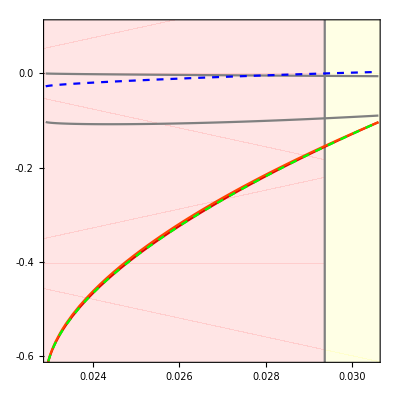

```mathematica
Show[
RegionPlot[x<0.02937,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Red, Opacity[0.1]}, PlotPoints->100],
RegionPlot[x>0.02937,{x,0,4},{y,-40,40}, BoundaryStyle->None,PlotStyle->{Yellow, Opacity[0.1]}],
TwoAxisPlot[{Re[T3SPL2/.stableT3SP],Re[T3SPL1/.stableT3SP]},{ds,0.0229,0.03061}],
(*Plot[Re[T3SPL1/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Red],*)
Plot[Re[T3SPL2/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->{Green,Dashed}],
Plot[Re[T3SPL3/.stableT3SP],{ds,0.0229,0.03061},PlotStyle->Gray],
Plot[Re[T3SPL4/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Gray],
Plot[Re[UL2T3SP/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->{Blue,Dashed}],
Frame->True,FrameTicks->{{{-0.6,-0.4,-0.2,{0.0,"0.0"}},{{-0.6,"-2.2"},{-0.4,"-2.1"},{-0.2,"-2.0"},{0.0,"-1.9"}}},{{0.024,0.026,0.028,{0.03,"0.030"}},None}},
FrameTicksStyle->{{Black,Red},{Automatic,Automatic}},
Axes->True,AxesOrigin->{0.023,0},
PlotRange->{{0.023,0.0305},{-0.6,0.1}},AspectRatio->1,LabelStyle->{16,Black}
]
```

### B

```mathematica
Show[
RegionPlot[x<0.02937,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Red, Opacity[0.1]}, PlotPoints->100],
RegionPlot[x>0.02937,{x,0,4},{y,-40,40},BoundaryStyle->None,PlotStyle->{Yellow, Opacity[0.1]},PlotPoints->250],
Plot[Re[J11T3SP/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Red],
Plot[Re[J22T3SP/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->{Dashed,Gray}],
Plot[Re[J33T3SP/.stableT3SP],{ds,0.0229,0.03061},PlotStyle->{Dotted,Gray}],
Plot[Re[J44T3SP/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Gray],
Plot[Re[T3SPL1/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->{Blue,Dashed}],
FrameTicks->{{{-2.5,{-2.0,"-2.0"},-1.5,{-1.0,"-1.0"},-0.5,{0.0,"0.0"}},None},{{0.024,0.026,0.028,{0.03,"0.030"}},None}},
Axes->True,AxesOrigin->{0.023,0},
PlotRange->{{0.023,0.0305},{-2.5,0.25}},AspectRatio->1,LabelStyle->{16,Black},Axes->True
]
```

-Graphics-

### C

```mathematica
Show[
RegionPlot[x<0.02937,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Red, Opacity[0.1]}, PlotPoints->100],
RegionPlot[x>0.02937,{x,0,4},{y,-40,40},BoundaryStyle->None,PlotStyle->{Yellow, Opacity[0.1]},PlotPoints->200],
Plot[Re[ConsResL2T3SP/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Green],
Plot[Re[EpidemL2T3SP/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Gray],
Plot[Re[T3SPL2/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->{Blue,Dashed}],
FrameTicks->{{{-0.8,-0.6,-0.4,-0.2,{0.0,"0.0"}, 0.2},None},{{0.024,0.026,0.028,{0.03,"0.030"}},None}},
Axes->True,AxesOrigin->{0.023,0},
PlotRange->{{0.023,0.0305},{-0.7,0.1}},AspectRatio->1,LabelStyle->{16,Black}
]
```

-Graphics-

### D

```mathematica
Show[
RegionPlot[x<0.02937,{x,0,4},{y,-40,40}, BoundaryStyle->{Gray},PlotStyle->{Red, Opacity[0.1]}, PlotPoints->100],
RegionPlot[x>0.02937,{x,0,4},{y,-40,40},BoundaryStyle->None,PlotStyle->{Yellow, Opacity[0.1]},PlotPoints->200],
Plot[Re[(J12T3SP*J21T3SP-J11T3SP*J22T3SP)/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->{Dashed,Gray}],
Plot[Re[(J13T3SP*J31T3SP-J11T3SP*J33T3SP)/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Gray],
Plot[Re[(-J11T3SP*J44T3SP)/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->Green],
Plot[Re[ConsResL2T3SP/.stableT3SP],{ds,0.0229,0.03061}, PlotStyle->{Blue,Dashed}],
FrameTicks->{{{-0.8,-0.6,-0.4,-0.2,{0.0,"0.0"}, 0.2},None},{{0.024,0.026,0.028,{0.03,"0.030"}},None}},
Axes->True,AxesOrigin->{0.023,0},
PlotRange->{{0.023,0.0305},{-0.7,0.1}},AspectRatio->1,LabelStyle->{16,Black}
]
```

-Graphics-